```mathematica
(*r=3,k=4,a=0.4,b=0.25,μ=0.5,m=0.2, and c=0.13,θ=0.2,α=0.06*)
(*r=1.5,k=6,a=1,b=0.02,μ=0.7,m=3.15, Allee IJBC sasmal *)
```

```mathematica
(*ρ=0.3;κ=35;δ=0.15;γ=0.02;α=0.7;μ=1.1;τ=0.1;
  ρ=0.3;κ=35;δ=0.06;γ=0.02;α=0.7;μ=1.5;τ=0.1;*)
```

#### Some calculations

```mathematica
F1[u_,v_]:=ρ*(1-u/κ)-(δ*v)/(1+δ*γ*u);
F2[u_,v_]:=ρ*(1-u/κ)*(u/τ-1)-(δ*v)/(1+δ*γ*u);
G[u_,v_]:=(α*δ*u)/(1+δ*γ*u)-μ;
```

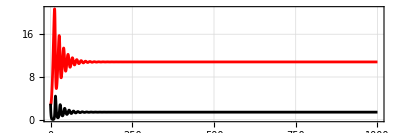

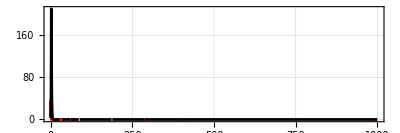

```mathematica
ρ=0.3;κ=35;δ=0.15;γ=0.02;α=0.7;μ=1.1;τ=0.1;
sol=NDSolve[{u'[t]==u[t]*F1[u[t],v[t]],v'[t]==v[t]*G[u[t],v[t]],u[0]==3,v[0]==3},{u,v},{t,0,1000}];
sol2=NDSolve[{u'[t]==u[t]*F2[u[t],v[t]],v'[t]==v[t]*G[u[t],v[t]],u[0]==3,v[0]==3},{u,v},{t,0,1000}];
A=Plot[Evaluate[{u[t],v[t]}/.sol],{t,0,1000},PlotRange->{All,{0,All}},GridLines->Automatic,AspectRatio->1/3,Frame->True,PlotStyle->{Red,Black}]
B=Plot[Evaluate[{u[t],v[t]}/.sol2],{t,0,1000},PlotRange->{All,{0,All}},GridLines->Automatic,AspectRatio->1/3,Frame->True,PlotStyle->{Red,Black}]
```

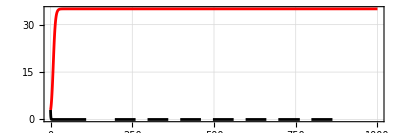

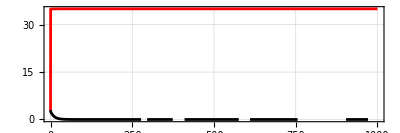

```mathematica
ρ=0.3;κ=35;δ=0.06;γ=0.02;α=0.7;μ=1.5;τ=0.1;
sol=NDSolve[{u'[t]==u[t]*F1[u[t],v[t]],v'[t]==v[t]*G[u[t],v[t]],u[0]==3,v[0]==3},{u,v},{t,0,1000}];
sol2=NDSolve[{u'[t]==u[t]*F2[u[t],v[t]],v'[t]==v[t]*G[u[t],v[t]],u[0]==3,v[0]==3},{u,v},{t,0,1000}];
A=Plot[Evaluate[{u[t],v[t]}/.sol],{t,0,1000},PlotRange->{All,{0,All}},GridLines->Automatic,AspectRatio->1/3,Frame->True,PlotStyle->{Red,Black}]
B=Plot[Evaluate[{u[t],v[t]}/.sol2],{t,0,1000},PlotRange->{All,{0,All}},GridLines->Automatic,AspectRatio->1/3,Frame->True,PlotStyle->{Red,Black}]
```

```mathematica
ρ=0.3;κ=35;δ=0.15;γ=0.02;α=0.7;μ=1.1;τ=0.1;
Solve[u[t]*F1[u[t],v[t]]==0&&v[t]*G[u[t],v[t]]==0,{u[t],v[t]}]
Solve[u[t]*F2[u[t],v[t]]==0&&v[t]*G[u[t],v[t]]==0,{u[t],v[t]}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{u[t]→10.8161,v[t]→1.42678},{u[t]→35.,v[t]→0.},{u[t]→0.,v[t]→0.}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{u[t]→0.1,v[t]→0.},{u[t]→10.8161,v[t]→152.895},{u[t]→35.,v[t]→0.},{u[t]→0.,v[t]→0.}}

```mathematica
ρ=0.3;κ=35;δ=0.06;γ=0.02;α=0.7;μ=1.5;τ=0.1;
Solve[u[t]*F1[u[t],v[t]]==0&&v[t]*G[u[t],v[t]]==0,{u[t],v[t]}]
Solve[u[t]*F2[u[t],v[t]]==0&&v[t]*G[u[t],v[t]]==0,{u[t],v[t]}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{u[t]→35.,v[t]→0.},{u[t]→37.3134,v[t]→-0.345288},{u[t]→0.,v[t]→0.}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{u[t]→0.1,v[t]→0.},{u[t]→35.,v[t]→0.},{u[t]→37.3134,v[t]→-128.494},{u[t]→0.,v[t]→0.}}

#### Main figures

```mathematica
initcond={10,10};
framelabels={Style["Prey density",16],Style["Predator density",16]};
```

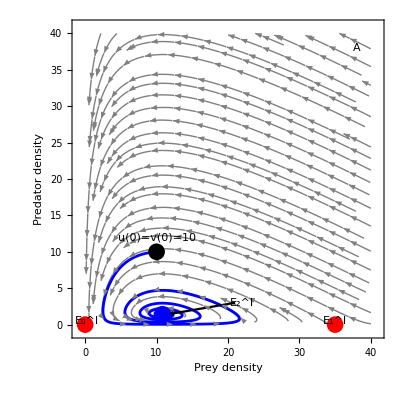

```mathematica
(*------------------------------Figure 2A------------------------------*)
ρ=0.3;κ=35;δ=0.15;γ=0.02;α=0.7;μ=1.1;τ=0.1;
data= Table[{{u,v},{u*F1[u,v],v*G[u,v]}},{u,0,40,0.5},{v,0,40,0.5}];
j=ListStreamPlot[data,StreamColorFunction->None,StreamStyle->Gray,PlotRange->{{-1,41},{-1,41}},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->framelabels];
{usol,vsol}={u[t],v[t]}/.Flatten[NDSolve[{u'[t]==u[t]*F1[u[t],v[t]],v'[t]==v[t]*G[u[t],v[t]],u[0]==initcond⟦1⟧,v[0]==initcond⟦2⟧},{u[t],v[t]},{t,0,200}]];
k=ParametricPlot[{{usol,vsol}},{t,0,200},AxesLabel->{"x","y"},PlotStyle->Directive[Blue,Thickness[0.005]]];
solutions=Select[NSolve[{F1[x,y]==0,G[x,y]==0},{x,y}],FreeQ[#,Complex]&];
solutionPoints={x,y}/. solutions;
p1=Graphics[{Blue,PointSize[0.03],Point[solutionPoints]}];
p2=Graphics[{Red,PointSize[0.03],Point[{0,0}]}];
p3=Graphics[{Red,PointSize[0.03],Point[{35,0}]}];
p4=Graphics[{Black,PointSize[0.03],Point[initcond]}];
q1=Graphics[{Arrowheads[0.05],Thickness[0.004],Arrow[{{21,3},{11.5,1.4}}]}];
A1=Show[j,k,p1,p2,p3,p4,q1,Epilog->{Style[Text["A",{38,38}],FontSize->20,Background->White],Style[Text["E_0^I",{0.2,0.5}],FontSize->14,Background->White],Style[Text["E_1^I",{35,0.5}],FontSize->14,Background->White],Style[Text["E_2^I",{22,3}],FontSize->14,Background->White],Style[Text["u(0)=v(0)=10",{10,12}],FontSize->16,Background->White]}]
```

```mathematica
Show[j,k,p1,p2,p3,p4,q1,Epilog->{Style[Text["A",{38,38}],FontSize->20,Background->White],Style[Text["E_0^I",{0.2,0.5}],FontSize->14,Background->White],Style[Text["E_1^I",{35,0.5}],FontSize->14,Background->White],Style[Text["E_2^I",{22,3}],FontSize->14,Background->White],Style[Text["u(0)=v(0)=10",{10,12}],FontSize->16,Background->White]}]
```

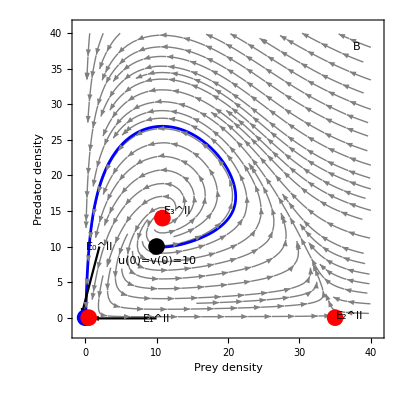

```mathematica
(*------------------------------Figure 2B------------------------------*)
ρ=0.3;κ=35;δ=0.15;γ=0.02;α=0.7;μ=1.1;τ=1;
data= Table[{{u,v},{u*F2[u,v],v*G[u,v]}},{u,0,40,1},{v,0,40,1}];
j=ListStreamPlot[data,StreamColorFunction->None,StreamStyle->Gray,PlotRange->{{-1,41},{-2,41}},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->framelabels];
{usol,vsol}={u[t],v[t]}/.Flatten[NDSolve[{u'[t]==u[t]*F2[u[t],v[t]],v'[t]==v[t]*G[u[t],v[t]],u[0]==initcond⟦1⟧,v[0]==initcond⟦2⟧},{u[t],v[t]},{t,0,100}]];
k=ParametricPlot[{{usol,vsol}},{t,0,50},AxesLabel->{"x","y"},PlotStyle->Directive[Blue,Thickness[0.005]]];
solutions=Select[NSolve[{F2[x,y]==0,G[x,y]==0},{x,y}],FreeQ[#,Complex]&];
solutionPoints={x,y}/. solutions;
p1=Graphics[{Red,PointSize[0.03],Point[solutionPoints]}];
p2=Graphics[{Blue,PointSize[0.03],Point[{0,0}]}];
p3=Graphics[{Red,PointSize[0.03],Point[{35,0}]}];
p4=Graphics[{Red,PointSize[0.03],Point[{0.5,0}]}];
p5=Graphics[{Black,PointSize[0.03],Point[initcond]}];
q2=Graphics[{Arrowheads[0.05],Thickness[0.004],Arrow[{{10,-0.1},{1,-0.1}}]}];
q4=Graphics[{Arrowheads[0.05],Thickness[0.004],Arrow[{{2,10},{-0.5,0.4}}]}];
A2=Show[j,k,p1,p2,p3,p4,p5,q2,q4,Epilog->{Style[Text["B",{38,38}],FontSize->20,Background->White],Style[Text["E_0^II",{2,10}],FontSize->14,Background->White],Style[Text["E_1^II",{10,-0.15}],FontSize->14,Background->None],Style[Text["E_2^II",{37,0.3}],FontSize->14,Background->White],Style[Text["E_3^II",{13,15}],FontSize->14,Background->White],Style[Text["u(0)=v(0)=10",{10,8}],FontSize->16,Background->White]}]
```

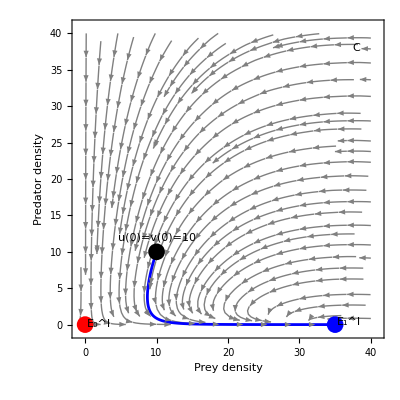

```mathematica
(*------------------------------Figure 2C------------------------------*)
ρ=0.3;κ=35;δ=0.06;γ=0.02;α=0.7;μ=1.5;τ=1;
data= Table[{{u,v},{u*F1[u,v],v*G[u,v]}},{u,-1,40,1},{v,0,40,1}];
j=ListStreamPlot[data,StreamColorFunction->None,StreamStyle->Gray,VectorScaling->None,PlotRange->{{-1,41},{-1,41}},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->framelabels];
{usol,vsol}={u[t],v[t]}/.Flatten[NDSolve[{u'[t]==u[t]*F1[u[t],v[t]],v'[t]==v[t]*G[u[t],v[t]],u[0]==initcond⟦1⟧,v[0]==initcond⟦2⟧},{u[t],v[t]},{t,0,200}]];
k=ParametricPlot[{{usol,vsol}},{t,0,200},AxesLabel->{"x","y"},PlotStyle->Directive[Blue,Thickness[0.005]]];
p2=Graphics[{Red,PointSize[0.03],Point[{0,0}]}];
p3=Graphics[{Blue,PointSize[0.03],Point[{35,0}]}];
p4=Graphics[{Black,PointSize[0.03],Point[initcond]}];
q2=Graphics[{Arrowheads[0.05],Thickness[0.004],Arrow[{{10,4},{3.5,3}}]}];
A3=Show[j,k,p2,p3,p4,Epilog->{Style[Text["C",{38,38}],FontSize->20,Background->White],Style[Text["E_0^I",{2,0.1}],FontSize->14,Background->White],Style[Text["E_1^I",{37,0.3}],FontSize->14,Background->White],Style[Text["u(0)=v(0)=10",{10,12}],FontSize->16,Background->White]}]
```

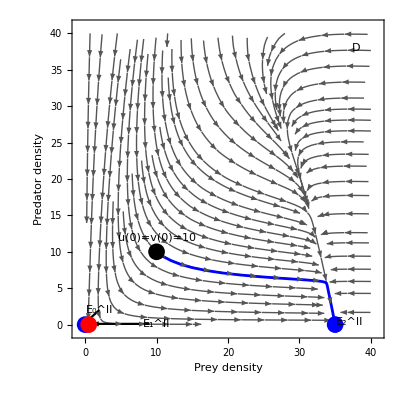

```mathematica
(*------------------------------Figure 2D------------------------------*)
ρ=0.3;κ=35;δ=0.06;γ=0.02;α=0.7;μ=1.5;τ=1;
data= Table[{{u,v},{u*F2[u,v],v*G[u,v]}},{u,0,40,0.5},{v,0,40,0.5}];
j=ListStreamPlot[data,StreamColorFunction->None,StreamStyle->Darker[Gray],PlotRange->{{-1,41},{-1,41}},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->framelabels];
{usol,vsol}={u[t],v[t]}/.Flatten[NDSolve[{u'[t]==u[t]*F2[u[t],v[t]],v'[t]==v[t]*G[u[t],v[t]],u[0]==initcond⟦1⟧,v[0]==initcond⟦2⟧},{u[t],v[t]},{t,0,200}]];
k=ParametricPlot[{{usol,vsol}},{t,0,200},AxesLabel->{"x","y"},PlotStyle->Directive[Blue,Thickness[0.005]]];
p2=Graphics[{Blue,PointSize[0.03],Point[{0,0}]}];
p3=Graphics[{Blue,PointSize[0.03],Point[{35,0}]}];
p4=Graphics[{Red,PointSize[0.03],Point[{0.5,0}]}];
p5=Graphics[{Black,PointSize[0.03],Point[initcond]}];
q2=Graphics[{Arrowheads[0.05],Thickness[0.004],Arrow[{{10,4},{3.5,3}}]}];
q3=Graphics[{Arrowheads[0.05],Thickness[0.004],Arrow[{{9,0.1},{1.0,0.1}}]}];
q4=Graphics[{Arrowheads[0.05],Thickness[0.004],Arrow[{{2,2},{-0.2,0.1}}]}];
A4=Show[j,k,p2,p3,p4,p5,q3,q4,Epilog->{Style[Text["D",{38,38}],FontSize->20,Background->White],Style[Text["E_0^II",{2,2}],FontSize->14,Background->White],Style[Text["E_1^II",{10,0.1}],FontSize->14,Background->White],Style[Text["E_2^II",{37,0.3}],FontSize->14,Background->White],Style[Text["u(0)=v(0)=10",{10,12}],FontSize->16,Background->White]}]
```